# Parâmetros nu - fit 2024 ( Far Detector )

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

## 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

## Without BG : ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_WithoutBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textPi = "DUNE_NSI_fit2D_WithoutBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
```

{{0.,0.000167494},{0.0005,0.00839568},{0.001,0.0395303},{0.0015,0.104852},{0.002,0.217837},{0.0025,0.393657},{0.003,0.649529},{0.0035,1.00345},{0.004,1.47487},{0.0045,2.08389},{0.005,2.85124},{0.0055,3.79785},{0.006,4.94478},{0.0065,6.31408},{0.007,7.9249},{0.0075,9.79946},{0.008,11.9562},{0.0085,14.417},{0.009,17.1976},{0.0095,20.3191},{0.01,23.797}}

{{0.,0.000167494},{0.0005,0.00578503},{0.001,0.018646},{0.0015,0.034659},{0.002,0.0522661},{0.0025,0.0725507},{0.003,0.0987776},{0.0035,0.136697},{0.004,0.19434},{0.0045,0.281367},{0.005,0.409398},{0.0055,0.591056},{0.006,0.841096},{0.0065,1.17445},{0.007,1.60756},{0.0075,2.15762},{0.008,2.84157},{0.0085,3.6765},{0.009,4.68139},{0.0095,5.87332},{0.01,7.27013}}

0.000167494

{{1}}

0.

0.000167494

{{1}}

0.

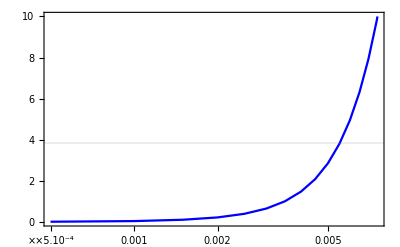

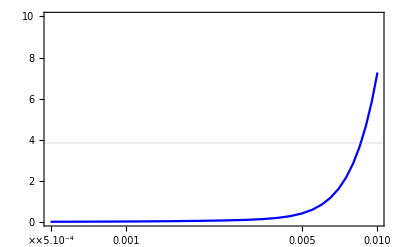

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue,
ScalingFunctions->{"Log10",None},PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Blue,
ScalingFunctions->{"Log10",None},PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* Without BG *)
plotWithoutBG=
Show[{PlotChi2NO},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
```

### For α:

In this case (No BG), the term α is added only by the systematic error!

## With BG : ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textPi = "DUNE_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
```

{{0.,0.000161804},{0.0005,0.0064636},{0.001,0.0312602},{0.0015,0.085001},{0.002,0.180275},{0.0025,0.331513},{0.003,0.555203},{0.0035,0.868834},{0.004,1.18059},{0.0045,1.61015},{0.005,2.18079},{0.0055,2.91413},{0.006,3.83206},{0.0065,4.95784},{0.007,6.31229},{0.0075,7.8291},{0.008,9.52816},{0.0085,11.5169},{0.009,13.8145},{0.0095,16.4446},{0.01,19.4263}}

{{0.,0.000161804},{0.0005,0.00411547},{0.001,0.0124702},{0.0015,0.0218004},{0.002,0.0311307},{0.0025,0.0419891},{0.003,0.0580749},{0.0035,0.0854462},{0.004,0.132467},{0.0045,0.209099},{0.005,0.327335},{0.0055,0.500257},{0.006,0.743229},{0.0065,1.07181},{0.007,1.50333},{0.0075,1.9876},{0.008,2.55927},{0.0085,3.27974},{0.009,4.16946},{0.0095,5.24783},{0.01,6.53482}}

0.000161804

{{1}}

0.

0.000161804

{{1}}

0.

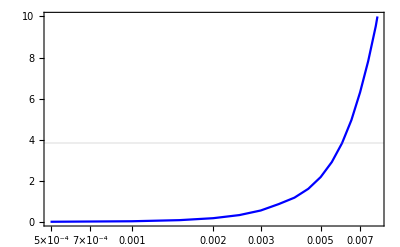

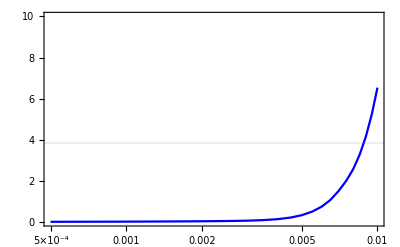

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListLogLinearPlot[DataMin, Joined->True, PlotStyle->Blue,PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListLogLinearPlot[DataMinPi, Joined->True, PlotStyle->Blue,
PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
```

### For α:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 2, 1];
newlis

textPi = "DUNE_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 2, 1];
newlisPi
```

{{-0.5,53.6242},{-0.45,42.2804},{-0.4,32.582},{-0.35,24.373},{-0.3,17.5259},{-0.25,11.9161},{-0.2,7.47672},{-0.15,4.13677},{-0.1,1.80464},{-0.05,0.444866},{0.,0.000161804},{0.05,0.508364},{0.1,2.00447},{0.15,4.44922},{0.2,7.80747},{0.25,12.0476},{0.3,17.1411},{0.35,23.062},{0.4,29.7868},{0.45,37.2939},{0.5,45.5638}}

{{-0.5,58.6619},{-0.45,46.3146},{-0.4,35.7709},{-0.35,26.8531},{-0.3,19.4123},{-0.25,13.3223},{-0.2,8.47108},{-0.15,4.79389},{-0.1,2.1294},{-0.05,0.523928},{0.,0.000161804},{0.05,0.464032},{0.1,1.89812},{0.15,4.28451},{0.2,7.5878},{0.25,11.7761},{0.3,16.8207},{0.35,22.6955},{0.4,29.3768},{0.45,36.8428},{0.5,45.0738}}

0.000161804

{{11}}

0.

0.000161804

{{11}}

0.

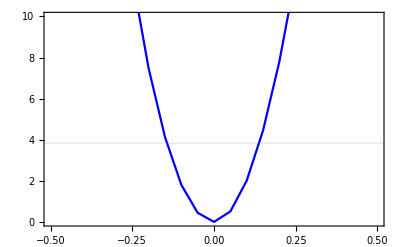

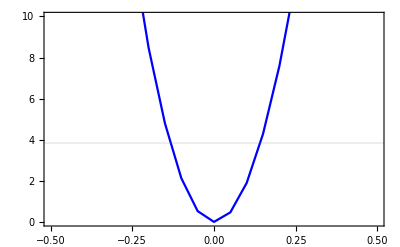

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Blue];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
```

# Antigo: parâmetros do artigo e não do nu - fit 2024 (não tem mais os arquivos)

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

#### 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

#### 3_Type - 1a : ϵ_μτ

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textBG = "DUNE_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.02,97.4686},{-0.018,66.9759},{-0.016,43.4369},{-0.014,26.1349},{-0.012,14.2283},{-0.01,6.75496},{-0.008,2.65317},{-0.006,0.820599},{-0.004,0.224584},{-0.002,0.069282},{0.,0.},{0.002,0.250498},{0.004,1.62595},{0.006,5.3147},{0.008,12.6424},{0.01,24.8827},{0.012,43.1547},{0.014,68.3934},{0.016,101.353},{0.018,142.626},{0.02,192.671}}

{{-0.02,89.9265},{-0.018,61.5855},{-0.016,39.8043},{-0.014,23.9194},{-0.012,12.908},{-0.01,6.04148},{-0.008,2.39015},{-0.006,0.682851},{-0.004,0.141326},{-0.002,0.0418864},{0.,0.},{0.002,0.205615},{0.004,1.27029},{0.006,4.09334},{0.008,9.9957},{0.01,20.1875},{0.012,35.5122},{0.014,57.06},{0.016,85.6268},{0.018,121.822},{0.02,166.123}}

##### Without_BG

0.

{{11}}

0.

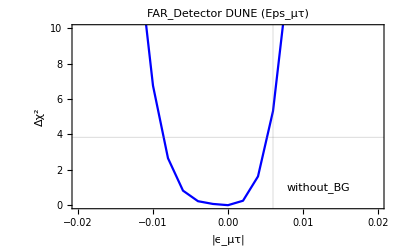

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

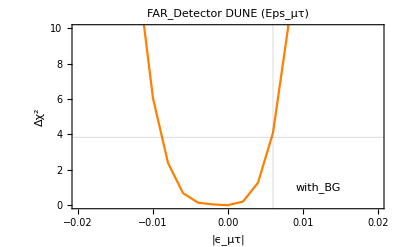

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

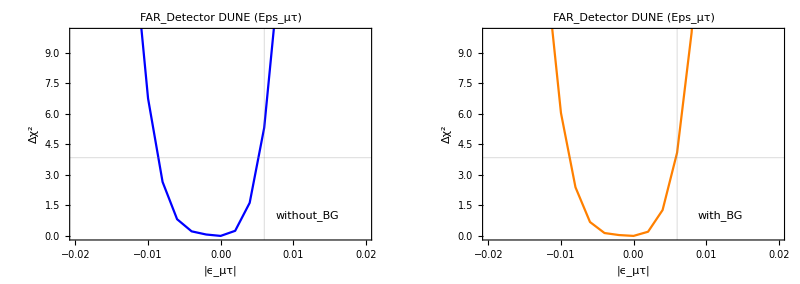

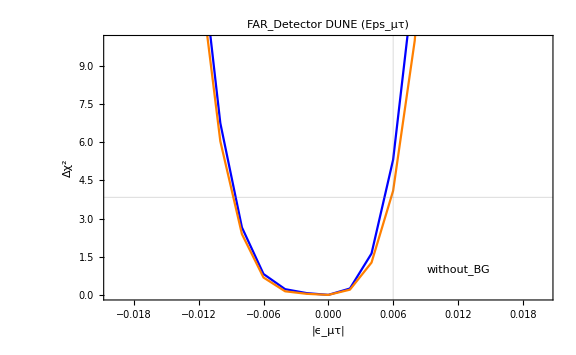

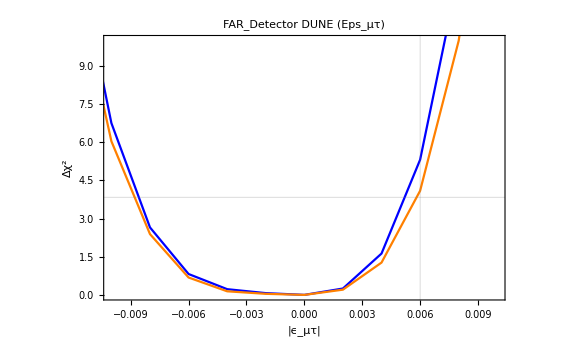

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
Show[plot,plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```

#### 3_Type - 1b : α

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];
text = "DUNE_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list,2, 1];
newlis

textBG = "DUNE_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,20.},{-0.45,16.2},{-0.4,12.8},{-0.35,9.8},{-0.3,7.2},{-0.25,5.},{-0.2,3.2},{-0.15,1.8},{-0.1,0.8},{-0.05,0.2},{0.,0.},{0.05,0.2},{0.1,0.8},{0.15,1.8},{0.2,3.2},{0.25,5.},{0.3,7.2},{0.35,9.8},{0.4,12.8},{0.45,16.2},{0.5,20.}}

{{-0.5,53.655},{-0.45,42.3566},{-0.4,32.4984},{-0.35,24.3179},{-0.3,17.677},{-0.25,11.9436},{-0.2,7.46182},{-0.15,4.23572},{-0.1,1.81532},{-0.05,0.473557},{0.,0.},{0.05,0.46523},{0.1,1.88231},{0.15,4.25342},{0.2,7.54303},{0.25,11.7192},{0.3,16.753},{0.35,22.6183},{0.4,29.2912},{0.45,36.7501},{0.5,44.975}}

##### Without_BG

0.

{{11}}

0.

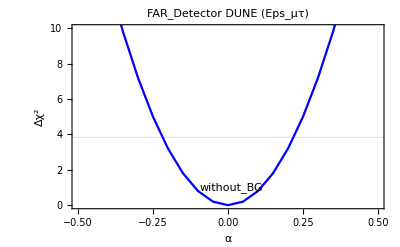

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

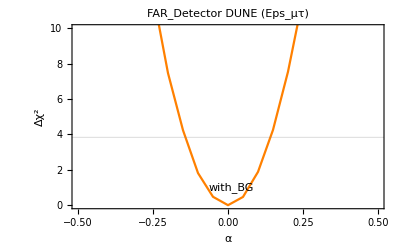

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

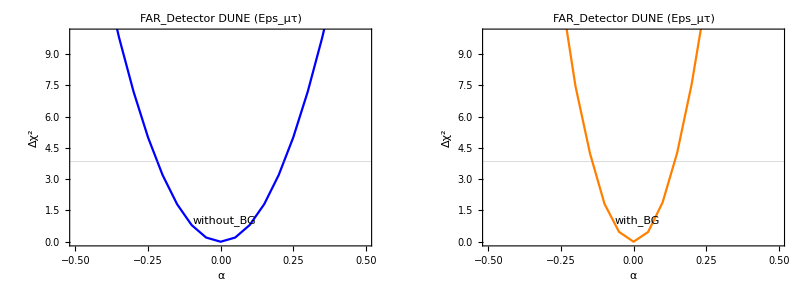

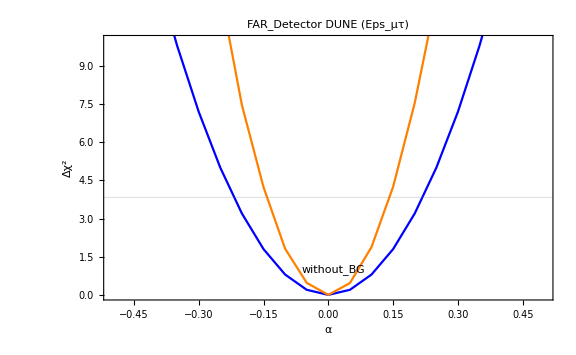

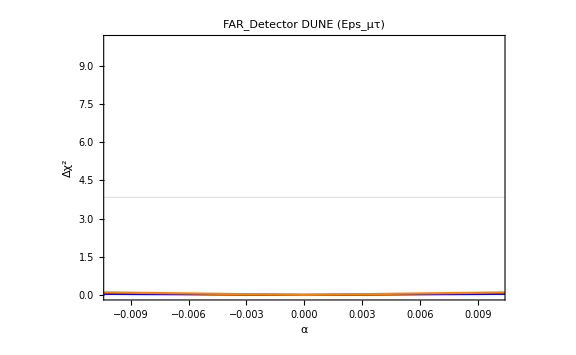

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
Show[plot,plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```

#### 3_Type - 2a : ϵ_μτ

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.02,89.9265},{-0.019,74.8987},{-0.018,61.5855},{-0.017,49.9139},{-0.016,39.8043},{-0.015,31.1256},{-0.014,23.8066},{-0.013,17.7647},{-0.012,12.8962},{-0.011,9.00299},{-0.01,6.04148},{-0.009,3.85963},{-0.008,2.31167},{-0.007,1.28852},{-0.006,0.682851},{-0.005,0.313176},{-0.004,0.141326},{-0.003,0.0729667},{-0.002,0.0418864},{-0.001,0.0160465},{0.,0.},{0.001,0.0366642},{0.002,0.205615},{0.003,0.528411},{0.004,1.21166},{0.005,2.34459},{0.006,4.09334},{0.007,6.57513},{0.008,9.9957},{0.009,14.4408},{0.01,20.0691},{0.011,27.0348},{0.012,35.4532},{0.013,45.4347},{0.014,57.06},{0.015,70.4247},{0.016,85.6268},{0.017,102.738},{0.018,121.822},{0.019,142.934},{0.02,166.123}}

##### With_BG

0.

{{21}}

0.

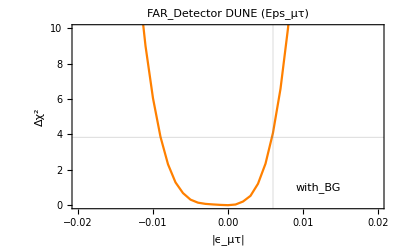

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

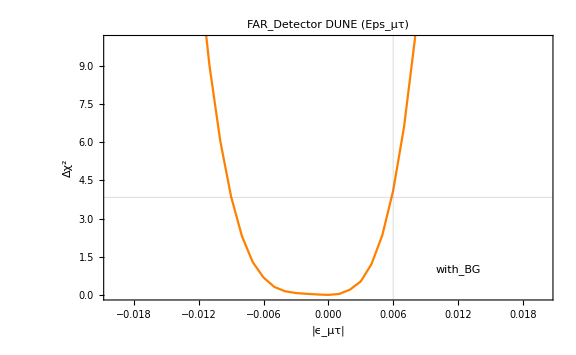

```mathematica
Show[plotBG,ImageSize->Large]
```

#### 3_Type - 2b : α

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,53.4784},{-0.475,47.5774},{-0.45,42.159},{-0.425,37.1989},{-0.4,32.4984},{-0.375,28.2077},{-0.35,24.3179},{-0.325,20.7662},{-0.3,17.4683},{-0.275,14.5279},{-0.25,11.9324},{-0.225,9.54079},{-0.2,7.46182},{-0.175,5.69659},{-0.15,4.12605},{-0.125,2.84378},{-0.1,1.81532},{-0.075,1.0069},{-0.05,0.452638},{-0.025,0.11315},{0.,0.},{0.025,0.111977},{0.05,0.460938},{0.075,1.05214},{0.1,1.88231},{0.125,2.95092},{0.15,4.25342},{0.175,5.78549},{0.2,7.54303},{0.225,9.52216},{0.25,11.7192},{0.275,14.1306},{0.3,16.753},{0.325,19.5832},{0.35,22.6183},{0.375,25.8552},{0.4,29.2912},{0.425,32.9237},{0.45,36.7501},{0.475,40.768},{0.5,44.975}}

##### With_BG

0.

{{21}}

0.

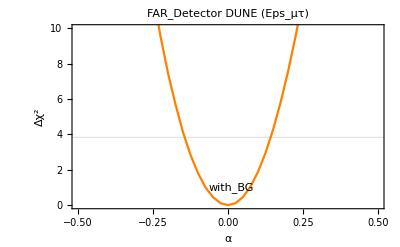

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

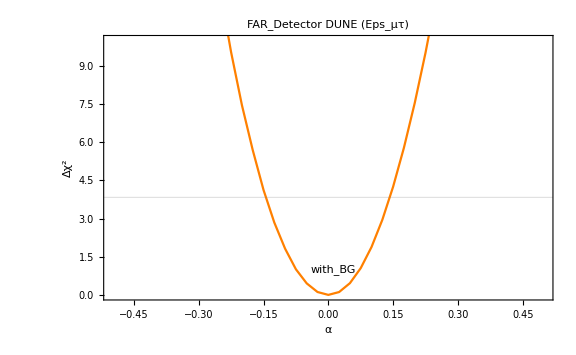

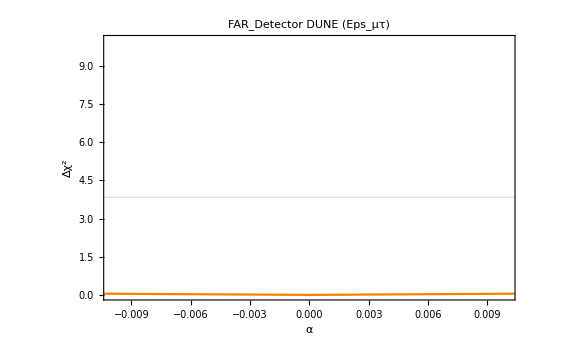

```mathematica
Show[plotBG,ImageSize->Large]
Show[plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```